```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pi/ext/repos/HASTE/testing/prevTrajectory

```mathematica
b=ReadList["trace_test.tst",Number,RecordLists->True];
b[[;;,2;;4]]=b[[;;,2;;4]]/1737.4;
a=ReadList["sat/sat_trace.txt",Number,RecordLists->True];
a[[;;,2;;4]]=a[[;;,2;;4]]/1737.4;
```

```mathematica
ListPointPlot3D[a[[;;,2;;4]],PlotStyle->Red,BoxRatios->{1, 1, 1},PlotRange->All,ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{b[[;;,2;;4]],a[[;;,2;;4]]},PlotStyle->{LightBlue,Red},BoxRatios->{1, 1, 1},PlotRange->All,ImageSize->Large]
```

-Graphics3D-

```mathematica
Manipulate[Show[
ListPointPlot3D[{b[[;;,2;;4]],a[[;;,2;;4]]},PlotStyle->{LightBlue,Red},PlotRange->Table[1.1{-Norm[a[[i,2;;4]]],Norm[a[[i,2;;4]]]},3],ImageSize->Large,BoxRatios->1,ViewPoint->{10,10,1}],
Graphics3D[{Opacity[0.6],Sphere[]}],
Graphics3D[{EdgeForm[Dashed],Opacity[0],Cylinder[{{0,0,-0.001},{0,0,0.001}}]}],
Graphics3D[{Black,Arrowheads[0.02],Arrow[{{0,0,0},a[[i,2;;4]]}]}]
],{i,1,Length[a],1}]
```

```mathematica
Manipulate[Show[
ListPointPlot3D[{b[[;;,2;;4]],a[[;;,2;;4]]},PlotStyle->{LightBlue,Red},PlotRange->Table[1.1{-Norm[a[[i,2;;4]]],Norm[a[[i,2;;4]]]},3],ImageSize->Large,BoxRatios->1,ViewPoint->{10,10,1}],
Graphics3D[{Black,Arrowheads[0.02],Arrow[{{0,0,0},a[[i,2;;4]]}]}]
],{i,1,Length[a],1}]
```

3 x^2-2 x^3

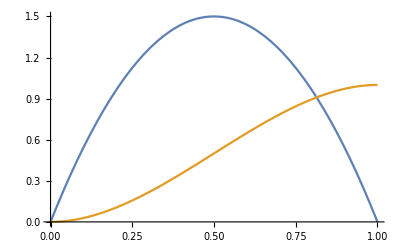

```mathematica
f2[x_]=-(2x-1)^2+1;
p2[x_]=f2[x]/Integrate[f2[x],{x,0,1}];
P2[x_]=Integrate[p2[xx],{xx,0,x}]
Plot[{p2[x],P2[x]},{x,0,1}]
```

5 x^2-10 x^3+10 x^4-4 x^5

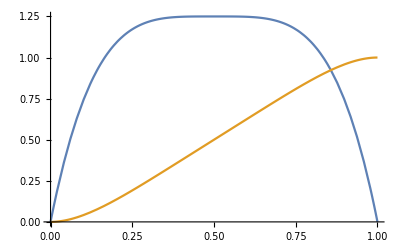

```mathematica
f4[x_]=-(2x-1)^4+1;
p4[x_]=f4[x]/Integrate[f4[x],{x,0,1}];
P4[x_]=Integrate[p4[xx],{xx,0,x}]
Plot[{p4[x],P4[x]},{x,0,1}]
```

7/6 (x+1/14 (-1-(-1+2 x)^7))

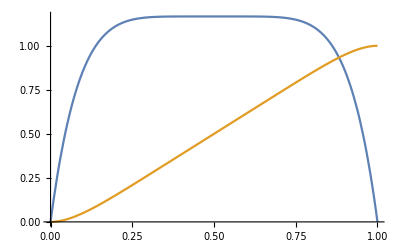

```mathematica
f6[x_]=-(2x-1)^6+1;
p6[x_]=f6[x]/Integrate[f6[x],{x,0,1}];
P6[x_]=Integrate[p6[xx],{xx,0,x}]
Plot[{p6[x],P6[x]},{x,0,1}]
```

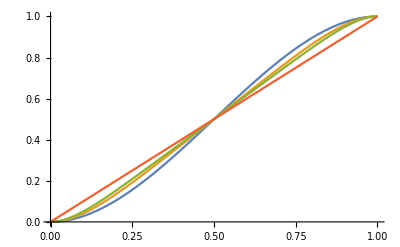

```mathematica
Plot[{P2[x],P4[x],P6[x],x},{x,0,1}]
```

```mathematica
HornerForm[P2[x]]
HornerForm[P4[x]]
HornerForm[P6[x]]
```

(3-2 x) x^2

x^2 (5+x (-10+(10-4 x) x))

x^2 (7+x (-70/3+x (140/3+x (-56+(112/3-(32 x)/3) x))))

```mathematica
P2[x]^2//FullSimplify
```

(3-2 x)^2 x^4